coordinate transformations:
single-particle   →  relative                : T
               relative  →  single-particle  : T^-1

```mathematica
nV=3;
spaceDim=3;
SingleToRelative={};

For[row=1,row<=nV,row++,{
AppendTo[SingleToRelative,
Table[Which[col==row&&row≠nV,-1,col==row+1,1,row==nV,1/nV,1==1,0],{col,1,nV}]
]
}];
Single=Array[Subscript["x", ##]&,{nV}];
Relative=Array[Subscript["r", ##+1,##]&,{nV-1}];AppendTo[Relative,"ρ"];
Tmat=SingleToRelative;
Tmatinv=Inverse[SingleToRelative];
Print[Relative//MatrixForm,"=",SingleToRelative//MatrixForm,"·",Single//MatrixForm,"=",SingleToRelative.Single//MatrixForm]
Print[Single//MatrixForm,"=",Tmatinv//MatrixForm,"·",Relative//MatrixForm,"=",Tmatinv.Relative//MatrixForm]
```

(r_(2,1)
r_(3,2)
ρ)=(-1 | 1 | 0
0 | -1 | 1
1/3 | 1/3 | 1/3)·(x_1
x_2
x_3)=(-x_1+x_2
-x_2+x_3
x_1/3+x_2/3+x_3/3)

(x_1
x_2
x_3)=(-2/3 | -1/3 | 1
1/3 | -1/3 | 1
1/3 | 2/3 | 1)·(r_(2,1)
r_(3,2)
ρ)=(ρ-(2 r_(2,1))/3-(r_(3,2))/3
ρ+(r_(2,1))/3-(r_(3,2))/3
ρ+(r_(2,1))/3+(2 r_(3,2))/3)

“Anarchy” diagram

```mathematica
ClearAll;
spaceDim=3;
AA={{t21^-1+(t32+t21)^-1,(t32+t21)^-1},{(t32+t21)^-1,t32^-1+(t32+t21)^-1}};iAA=Simplify[Inverse[AA]];
A3=KroneckerProduct[AA,IdentityMatrix[spaceDim]];
iA3=Simplify[Inverse[A3]];
Print["A = ",A3//MatrixForm,"  A^-1 = ",iA3//MatrixForm,"  Det(A) = ",Simplify[Det[A3]]//MatrixForm];
Print[Simplify[((t21 (t32+t21) t32)^(-spaceDim)/Det[A3])^(1/2)]];
```

A = (1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0
0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0
0 | 0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32)
1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32) | 0 | 0
0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32) | 0
0 | 0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32))  A^-1 = ((t21 (t21+2 t32))/(2 (t21+t32)) | 0 | 0 | -(t21 t32)/(2 (t21+t32)) | 0 | 0
0 | (t21 (t21+2 t32))/(2 (t21+t32)) | 0 | 0 | -(t21 t32)/(2 (t21+t32)) | 0
0 | 0 | (t21 (t21+2 t32))/(2 (t21+t32)) | 0 | 0 | -(t21 t32)/(2 (t21+t32))
-(t21 t32)/(2 (t21+t32)) | 0 | 0 | (t32 (2 t21+t32))/(2 (t21+t32)) | 0 | 0
0 | -(t21 t32)/(2 (t21+t32)) | 0 | 0 | (t32 (2 t21+t32))/(2 (t21+t32)) | 0
0 | 0 | -(t21 t32)/(2 (t21+t32)) | 0 | 0 | (t32 (2 t21+t32))/(2 (t21+t32)))  Det(A) = 8/(t21^3 t32^3)

(√(1/(t21+t32)^3))/(2 √2)

```mathematica
jvec={0 I p1,I pp1};
iAA2=1/(4 τ) {{(τ-t/2) (3 τ+t/2),-τ^2+t^2},{-τ^2+t^2,(τ+t/2) (3 τ+t/2)}};
jvec//MatrixForm
iAA//MatrixForm
iAA2//MatrixForm
Print[Apart[Simplify[jvec.iAA.jvec]]," = ",Simplify[jvec.iAA.jvec]]
Apart[Simplify[jvec.iAA2.jvec]]
```

(0
ⅈ pp1)

((t21 (t21+2 t32))/(2 (t21+t32)) | -(t21 t32)/(2 (t21+t32))
-(t21 t32)/(2 (t21+t32)) | (t32 (2 t21+t32))/(2 (t21+t32)))

(((-t/2+τ) (t/2+3 τ))/(4 τ) | (t^2-τ^2)/(4 τ)
(t^2-τ^2)/(4 τ) | ((t/2+τ) (t/2+3 τ))/(4 τ))

-(pp1^2 t21)/2-(pp1^2 t32)/2+(pp1^2 t21^2)/(2 (t21+t32)) = -(pp1^2 t32 (2 t21+t32))/(2 (t21+t32))

-(pp1^2 t)/2-(pp1^2 t^2)/(16 τ)-(3 pp1^2 τ)/4

```mathematica
Simplify[Integrate[x^(-1/2) Exp[-α x],{x,0,Infinity}]]
```

ConditionalExpression[(√π)/(√α),Re[α]>0]

“Fish-slash” diagram

```mathematica
ClearAll;
AA={{t21^-1+(t32+t21)^-1,(t32+t21)^-1,0},{(t32+t21)^-1,t32^-1+(t32+t21)^-1+(t43+t32)^-1,(t43+t32)^-1},{0,(t43+t32)^-1,(t43+t32)^-1+t43^-1}};iAA=Simplify[Inverse[AA]];
A3=KroneckerProduct[AA,IdentityMatrix[spaceDim]];
iA3=Simplify[Inverse[A3]];
Print["A = ",A3//MatrixForm,"  A^-1 = ",iA3//MatrixForm,"  Det(A) = ",Simplify[Det[A3]]//MatrixForm];
Print[Simplify[(((t32+t21) t21 t32 t43 (t43+t32))^(-spaceDim)/Det[A3])^(1/2)]];
```

A = (1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0
0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0
0 | 0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0
1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43) | 0 | 0 | 1/(t32+t43) | 0 | 0
0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43) | 0 | 0 | 1/(t32+t43) | 0
0 | 0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43) | 0 | 0 | 1/(t32+t43)
0 | 0 | 0 | 1/(t32+t43) | 0 | 0 | 1/t43+1/(t32+t43) | 0 | 0
0 | 0 | 0 | 0 | 1/(t32+t43) | 0 | 0 | 1/t43+1/(t32+t43) | 0
0 | 0 | 0 | 0 | 0 | 1/(t32+t43) | 0 | 0 | 1/t43+1/(t32+t43))  A^-1 = ((t21 (2 t21 (t32+t43)+t32 (3 t32+4 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0
0 | (t21 (2 t21 (t32+t43)+t32 (3 t32+4 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0
0 | 0 | (t21 (2 t21 (t32+t43)+t32 (3 t32+4 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43))
-(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t32 (2 t21+t32) (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0
0 | -(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t32 (2 t21+t32) (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0
0 | 0 | -(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t32 (2 t21+t32) (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43))
(t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t43 (2 t21 (2 t32+t43)+t32 (3 t32+2 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0
0 | (t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t43 (2 t21 (2 t32+t43)+t32 (3 t32+2 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0
0 | 0 | (t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | 0 | 0 | (t43 (2 t21 (2 t32+t43)+t32 (3 t32+2 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)))  Det(A) = (4 t21 (t32+t43)+t32 (3 t32+4 t43))^3/(t21^3 t32^3 (t21+t32)^3 t43^3 (t32+t43)^3)

√(1/(4 t21 (t32+t43)+t32 (3 t32+4 t43))^3)

```mathematica
jvec={I (-3/4 (p1+p2)+1/4 p3-1/4 pp1-1/4 (pp2+pp3)),I (-2/4 (p1+p2)-2/4 p3-2/4 pp1-2/4 (pp2+pp3)),I (-1/4 (p1+p2)-1/4 p3+1/4 pp1-3/4 (pp2+pp3))};
jvecm={I p1,0,I pp1};
iAA//MatrixForm
expo=Simplify[jvec.iA3.jvec,Assumptions->{p1+p2+p3==pp1+pp2+pp3}]
PolynomialReduce[Numerator[expo],Denominator[expo],{t43,t32,t21}]
```

((t21 (2 t21 (t32+t43)+t32 (3 t32+4 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | -(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | (t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43))
-(t21 t32 (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | (t32 (2 t21+t32) (t32+2 t43))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43))
(t21 t32 t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | -(t32 (2 t21+t32) t43)/(4 t21 (t32+t43)+t32 (3 t32+4 t43)) | (t43 (2 t21 (2 t32+t43)+t32 (3 t32+2 t43)))/(4 t21 (t32+t43)+t32 (3 t32+4 t43)))

-1/(4 t21 (t32+t43)+t32 (3 t32+4 t43))(2 pp1 (pp2+pp3) (2 t21^2+3 t21 t32+t32^2) (t32+t43)+pp1^2 (t21+t32) (2 t21 (t32+t43)+t32 (t32+2 t43))+p3^2 t21 (2 t21 (t32+t43)+t32 (3 t32+4 t43))+(pp2+pp3)^2 (2 t21^2 (t32+t43)+t32 (t32^2+3 t32 t43+2 t43^2)+t21 (3 t32^2+6 t32 t43+2 t43^2))-2 p3 t21 (2 pp1 (t21+t32) (t32+t43)+(pp2+pp3) (2 t21 (t32+t43)+t32 (2 t32+3 t43))))

{{1/8 (-8 p3^2+8 p3 pp1-4 pp1^2+12 p3 pp2-8 pp1 pp2-5 pp2^2+12 p3 pp3-8 pp1 pp3-10 pp2 pp3-5 pp3^2) t21+1/8 (-4 pp1^2-4 pp1 pp2-3 pp2^2-4 pp1 pp3-6 pp2 pp3-3 pp3^2) t32+1/2 (-pp2^2-2 pp2 pp3-pp3^2) t43},1/2 (4 p3^2-4 p3 pp2+pp2^2-4 p3 pp3+2 pp2 pp3+pp3^2) t21^2 t32+1/8 (8 p3 pp1+4 pp1^2-4 p3 pp2-8 pp1 pp2+3 pp2^2-4 p3 pp3-8 pp1 pp3+6 pp2 pp3+3 pp3^2) t21 t32^2+1/8 (4 pp1^2-4 pp1 pp2+pp2^2-4 pp1 pp3+2 pp2 pp3+pp3^2) t32^3+1/2 (4 p3^2-4 p3 pp2+pp2^2-4 p3 pp3+2 pp2 pp3+pp3^2) t21^2 t43}

```mathematica
PolynomialReduce[a x^2+b x+c,d x+e,x]
```

{{(b d-a e)/d^2+(a x)/d},(c d^2-b d e+a e^2)/d^2}

“Gauss-Fish” diagram

```mathematica
ClearAll;
AA={{t21^-1+(t32+t21)^-1,(t32+t21)^-1,0,0,0},{(t32+t21)^-1,t32^-1+(t32+t21)^-1+(t54+t43+t32)^-1,(t54+t43+t32)^-1,(t54+t43+t32)^-1,0},{0,(t54+t43+t32)^-1,(t54+t43+t32)^-1+t43^-1+t43^-1,(t54+t43+t32)^-1,0},{0,(t54+t43+t32)^-1,(t54+t43+t32)^-1,(t54+t43+t32)^-1+(t65+t54)^-1+t54^-1,(t65+t54)^-1},{0,0,0,(t65+t54)^-1,(t65+t54)^-1+t65^-1}};iAA=Simplify[Inverse[AA]];
(*Print["A = ",AA//MatrixForm,"  A^-1 = ",iAA//MatrixForm,"  Det(A) = ",Simplify[Det[AA]]//MatrixForm];*)
A3=KroneckerProduct[AA,IdentityMatrix[3]];
iA3=Simplify[Inverse[A3]];
Print["A_(3  D) = ",A3//MatrixForm,"  Det(A_(3  D)) = ",Simplify[Det[A3]]//MatrixForm];
Print[Simplify[(((t32+t21) t21 t32 t43 t43 t54 t65(t54+t43+t32) (t65+t54))^3 Det[A3])^(-1/2)]];
```

A_(3  D) = (1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/t21+1/(t21+t32) | 0 | 0 | 1/(t21+t32) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0 | 0
0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0
0 | 0 | 1/(t21+t32) | 0 | 0 | 1/t32+1/(t21+t32)+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0
0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 2/t43+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 2/t43+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 2/t43+1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 0
0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/t54+1/(t32+t43+t54)+1/(t54+t65) | 0 | 0 | 1/(t54+t65) | 0 | 0
0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/t54+1/(t32+t43+t54)+1/(t54+t65) | 0 | 0 | 1/(t54+t65) | 0
0 | 0 | 0 | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/(t32+t43+t54) | 0 | 0 | 1/t54+1/(t32+t43+t54)+1/(t54+t65) | 0 | 0 | 1/(t54+t65)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(t54+t65) | 0 | 0 | 1/t65+1/(t54+t65) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(t54+t65) | 0 | 0 | 1/t65+1/(t54+t65) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(t54+t65) | 0 | 0 | 1/t65+1/(t54+t65))  Det(A_(3  D)) = (64 (t32 (3 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65))+t21 (4 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65)))^3)/(t21^3 t32^3 (t21+t32)^3 t43^3 t54^3 (t32+t43+t54)^3 t65^3 (t54+t65)^3)

1/(8 √(t43^3 (t32 (3 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65))+t21 (4 t32 (t54+t65)+3 t43 (t54+t65)+t54 (3 t54+4 t65)))^3))

```mathematica
Amat={{1,0,0},{0,1,0},{0,0,1}};Print["A = ",Amat//MatrixForm,"   A^-1 = ",Simplify[Inverse[Amat]]//MatrixForm,"   Det(A) = ",Simplify[Det[Amat]]//MatrixForm];
Simplify[(Inverse[Amat][[1,1]] Inverse[Amat][[2,2]] Inverse[Amat][[3,3]]+Inverse[Amat][[1,2]] Inverse[Amat][[2,1]] Inverse[Amat][[3,3]]+Inverse[Amat][[1,1]] Inverse[Amat][[2,3]] Inverse[Amat][[3,2]]+Inverse[Amat][[1,3]] Inverse[Amat][[2,2]] Inverse[Amat][[3,1]]+Inverse[Amat][[1,2]] Inverse[Amat][[2,3]] Inverse[Amat][[3,1]]) ((2 π)^(3/2)/√Det[Amat])]
Integrate[x^2 y^2 z^2 Exp[-1/2(Expand[{x,y,z}.Amat.{x,y,z}])],{x,0,Infinity},{y,0,Infinity},{z,0,Infinity}]
```

A = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)   A^-1 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)   Det(A) = 1

2 √2 π^(3/2)

π^(3/2)/(2 √2)

```mathematica
spacedim=1;
ami=KroneckerProduct[{{a,-a},{-a,a}},IdentityMatrix[spacedim]];
ami//MatrixForm
```

(a | -a
-a | a)

```mathematica
Sum[q^n p^m,{n,0,Infinity},{m,0,Infinity},Assumptions->{q<1,p<1}]
```

1/((1-p) (1-q))

```mathematica
bsu[ϵ_,E_]:=Integrate[t^(-0/2) Exp[-t E],{t,ϵ,Infinity},Assumptions->{ϵ>0,E>0}];
bsu[λ,ee]
Integrate[t^(-0/2) Exp[-t ee],t,Assumptions->ee>0]
```

ⅇ^(-ee λ)/ee

-ⅇ^(-ee t)/ee

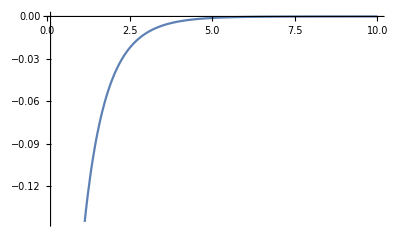

```mathematica
t=1;
Plot[-(2/(E^(EE*t)*Sqrt[t])) + (2*Sqrt[EE*t]*Gamma[1/2, EE*t])/Sqrt[t],{EE,0.1,10},PlotPoints->10]
```

Power::infy: Infinite expression 1/0. encountered.

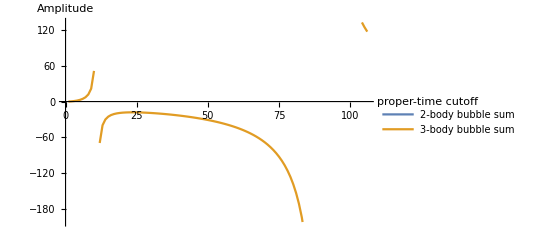

```mathematica
a=2;
tr=Range[0,10.5,0.1];
bub2=C Sum[(C/(√ϵ))^n,{n,0,Infinity}]/.{ϵ->tr,C->1/(a+ϵ^(-1/2))};
bub3=C^2 Sum[(3^(n+2)-3) (C/(√ϵ))^n,{n,0,Infinity}]/.{C->1,ϵ->tr};
ListPlot[{bub2,bub3},Joined->True,PlotLegends->{"2-body bubble sum","3-body bubble sum"},AxesLabel->{"proper-time cutoff","Amplitude"}]
```

```mathematica
al=as;
renbub2=Simplify[I C Sum[((I C)/(√ϵ))^n,{n,0,Infinity}]/.{C->1/(al+ϵ^(-1/2))}]
renbub3=Simplify[C^2 Sum[(3^(n+2)-3) ((I C)/(√ϵ))^n,{n,0,Infinity}]/.{C->1/(al+ϵ^(-1/2))}]
(*ListPlot[{Transpose[{tr,Table[renbub2,{ϵ,tr}]}],Transpose[{tr,renbub3/.ϵ->tr}]},Joined->True,PlotLegends->{"2-body bubble sum","3-body bubble sum"},AxesLabel->{"proper-time cutoff","Amplitude"}]*)
```

(ⅈ √ϵ)/((1-ⅈ)+as √ϵ)

(6 ϵ)/((-2-4 ⅈ)+(2-4 ⅈ) as √ϵ+as^2 ϵ)

```mathematica
sols=Solve[3 ϵ^-1-4 C^-1 ϵ^(-1/2)+C^-2-6 a3==0,C]
```

{{C→(-2 √ϵ-√(ϵ+6 a3 ϵ^2))/(3 (-1+2 a3 ϵ))},{C→(-2 √ϵ+√(ϵ+6 a3 ϵ^2))/(3 (-1+2 a3 ϵ))}}

{(2 ϵ+√ϵ √(ϵ (1+18 ϵ)))/(√ϵ-18 ϵ^(3/2)-√(ϵ (1+18 ϵ))),(2 ϵ-√ϵ √(ϵ (1+18 ϵ)))/(√ϵ-18 ϵ^(3/2)+√(ϵ (1+18 ϵ)))}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

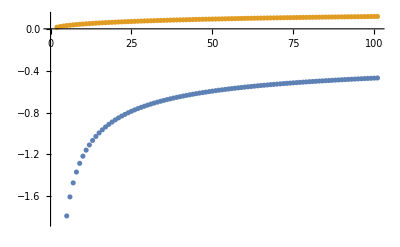

```mathematica
a3=3;
tmp2=Simplify[C Sum[(C/(√ϵ))^n,{n,0,Infinity}]/.sols]
ListPlot[tmp2/.ϵ->tr]
```

```mathematica
amat={{a+b+2 c,-2 c},{-2 c,d+e+2 c}};svec={x1 a+x2 b,x3 e+x4 d};
amat//MatrixForm
svec//MatrixForm
```

(a+b+2 c | -2 c
-2 c | 2 c+d+e)

(a x1+b x2
e x3+d x4)

```mathematica
Simplify[svec.Inverse[amat].svec]//MatrixForm
```

(a^2 (2 c+d+e) x1^2+2 a b (2 c+d+e) x1 x2+b^2 (2 c+d+e) x2^2+2 c (e x3+d x4)^2+a (e x3+d x4) (4 c x1+e x3+d x4)+b (e x3+d x4) (4 c x2+e x3+d x4))/(2 c (d+e)+a (2 c+d+e)+b (2 c+d+e))

```mathematica
Det[amat]
```

2 a c+2 b c+a d+b d+2 c d+a e+b e+2 c e

```mathematica
Integrate[τ^(-n/2) Exp[-τ α],{τ,ϵ,Infinity},Assumptions->{ϵ>0,α>0,n∈Integers,n>0}]
```

α^(-1+n/2) Gamma[1-n/2,α ϵ]

```mathematica
Integrate[q^2/(α-q^2),{q,0,ϵ},Assumptions->{ϵ>0,α>0}]
```

ConditionalExpression[-ϵ+1/2 √α Log[(√α+ϵ)/(√α-ϵ)],α>ϵ^2]

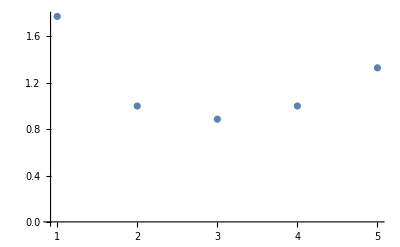

```mathematica
ListPlot[Gamma[#/2]&@Range[5],PlotRange->Full]
```

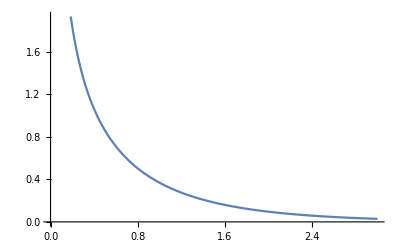

```mathematica
Plot[ϵ^(-1/2)Exp[-ϵ],{ϵ,0,3}]
```

```mathematica
Series[Exp[-E ϵ],{ϵ,0,2}]
```

1-ⅇ ϵ+(ⅇ^2 ϵ^2)/2+O[ϵ]^3

```mathematica
Simplify[4 (ρ-2/3 r1-1/3 r2) (2 ρ+2/3 r1+1/3 r2)+(ρ+1/3 r1-1/3 r2) (ρ+7/3 r1+5/3 r2)]
```

-r1^2-2 r1 r2-r2^2+9 ρ^2

```mathematica
expo=-(-2 p1 pp1 t21 t32+pp1^2 t32 (2 t21+t32)+p1^2 t21 (t21+2 t32))/(2 m (t21+t32));
Apart[expo]
```

-((2 p1^2-2 p1 pp1+pp1^2) t21)/(2 m)-(pp1^2 t32)/(2 m)+(p1^2 t21^2-2 p1 pp1 t21^2+pp1^2 t21^2)/(2 m (t21+t32))

```mathematica
Integrate[(τ)^(-3/2) Exp[-a τ+b/τ],{τ,0,Infinity},Assumptions->{ϵ>0,a>0,b>0}]
```

(ⅇ^(-2 ⅈ √(a b)) √π (-ⅈ+ⅇ^(4 ⅈ √(a b)) (ⅈ+Erfi[√(b/ϵ)-ⅈ √(a ϵ)])+Erfi[√(b/ϵ)+ⅈ √(a ϵ)]))/(2 √b)

```mathematica
eqn=a (1/x+1/(x+y))+b (1/y+1/(x+y))-(1/(x+y))==0;
Solve[eqn,{a,b}]
```

{{b→y/(x+2 y)-(a y (2 x+y))/(x (x+2 y))}}

```mathematica
AA//MatrixForm
Eigensystem[AA]
```

(1/t21+1/(t21+t32) | 1/(t21+t32)
1/(t21+t32) | 1/t32+1/(t21+t32))

{{2/(t21+t32),(t21+t32)/(t21 t32)},{{-t21/t32,1},{t32/t21,1}}}